# Análisis Práctica 10

```mathematica
DSolve[y'[x]== y[x], y[x], x]
```

{{y[x]→ⅇ^x C[1]}}

COGER DE DOCENCIA


RESONANCIA:

```mathematica
Clear[y]
```

```mathematica
DSolve[{y''[x] + y[x] == 1, y[0] == 0, y'[0] == 1}, y[x], x]
```

{{y[x]→1-Cos[x]+Sin[x]}}

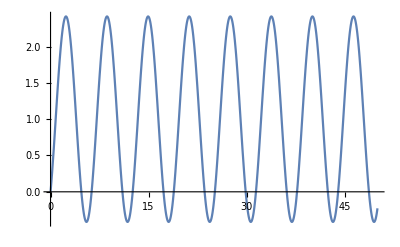

```mathematica
{{y[x]->1-Cos[x]+Sin[x]}}

Plot[{1-Cos[x]+Sin[x]}, {x, 0, 50}]
```

```mathematica
DSolve[{y''[x] + y[x] == Cos [a x], y[0] == 0, y'[0] == 1}, y[x], x]
```

```mathematica
{{y[x]->(Cos[x]-Cos[x]^2 Cos[a x]-Sin[x]+a^2 Sin[x]-Cos[a x] Sin[x]^2)/(-1+a^2)}}

Manipulate[Plot[(Cos[x]-Cos[x]^2 Cos[a x]-Sin[x]+a^2 Sin[x]-Cos[a x] Sin[x]^2)/(-1+a^2), {x, 0, 100}], {a, 0, 2}]
```

{{y[x]→(Cos[x]-Cos[x]^2 Cos[a x]-Sin[x]+a^2 Sin[x]-Cos[a x] Sin[x]^2)/(-1+a^2)}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.